```mathematica
Clear["Global`*"]
```

## import TPCs and trait data

{RGBColor[0.6509803921568628, 0.807843137254902, 0.8901960784313725],RGBColor[0.12156862745098039, 0.47058823529411764, 0.7058823529411765],RGBColor[0.01568627450980392, 0.24705882352941178, 0.4392156862745098],RGBColor[0.2, 0.6274509803921569, 0.17254901960784313],RGBColor[0.27450980392156865, 0.8588235294117647, 0.7411764705882353],RGBColor[0.984313725490196, 0.6039215686274509, 0.6],RGBColor[0.8901960784313725, 0.10196078431372549, 0.10980392156862745],RGBColor[0.5490196078431373, 0.06274509803921569, 0.1607843137254902],RGBColor[1., 0.8352941176470589, 0.],RGBColor[0.7764705882352941, 0.5764705882352941, 0.32941176470588235],RGBColor[1., 0.4980392156862745, 0.],RGBColor[0.788235294117647, 0.09019607843137255, 0.592156862745098],RGBColor[0.792156862745098, 0.6980392156862745, 0.8392156862745098],RGBColor[0.41568627450980394, 0.23921568627450981, 0.6039215686274509]}

Empirical TPC parameters:

Species | a | E_a | E_d | Th | T_opt
Paramecium bursaria | 2.32518 | 0.0118192 | 3.04 | 315.024 | 300.187
Paramecium multimicronucleatum | 2.32217 | 0.0239634 | 4.55346 | 312.64 | 303.254
Euplotes sp. | 2.33323 | 0.0442073 | 3.00699 | 312.567 | 301.243
Blepharisma sp. | 2.33053 | 0.0177519 | 4.0474 | 315.676 | 304.592
Urocentrum turbo | 2.37256 | 0.045334 | 3.50638 | 306.889 | 297.191
Colpidium striatum | 2.49857 | 0.0888437 | 1.27075 | 309.442 | 293.533
Paramecium aurelia | 2.51421 | 0.141601 | 1.2094 | 310.791 | 297.507
Paramecium caudatum | 2.40149 | 0.0867487 | 6.12682 | 305.36 | 299.905
Tillina magna | 2.39267 | 0.069512 | 1.9241 | 319.587 | 305.267
Halteria grandinella | 2.49703 | 0.107839 | 2.82976 | 306.101 | 297.176
Cyclidium glaucoma | 2.51221 | 0.0851891 | 7.15525 | 306.146 | 301.248
Colpoda steinii | 2.61698 | 0.140333 | 3.88433 | 306.294 | 299.622
Glaucoma sp. | 2.63053 | 0.140107 | 4.96194 | 305.956 | 300.321
Tetrahymena pyriformis | 2.56778 | 0.134055 | 12.2966 | 308.368 | 305.399

Trait-based (predicted) TPC parameters:

Species | Biovolume_Spheroid_GEO | Geodesic_Aspect_Ratio | Sigma.Intensity | a | E_a | E_d | Th | T_opt | est_a | est_Ea | est_Ed | est_Th | est_K22
Paramecium bursaria | 5.07416 | -0.613943 | 1.53757 | 2.32518 | 0.0118192 | 3.04 | 315.024 | 300.187 | 2.41443 | 0.0828515 | 3.52036 | 311.257 | 64.1009
Paramecium multimicronucleatum | 5.45261 | -0.784922 | 1.48043 | 2.32217 | 0.0239634 | 4.55346 | 312.64 | 303.254 | 2.33954 | 0.0551357 | 2.91049 | 313.887 | 56.4758
Euplotes sp. | 5.1445 | -0.906208 | 1.56813 | 2.33323 | 0.0442073 | 3.00699 | 312.567 | 301.243 | 2.38963 | 0.0976754 | 3.407 | 308.467 | 44.7141
Blepharisma sp. | 4.58179 | -0.854642 | 1.3847 | 2.33053 | 0.0177519 | 4.0474 | 315.676 | 304.592 | 2.3343 | 0.00870364 | 4.3138 | 313.832 | 251.16
Urocentrum turbo | 4.51687 | -0.385428 | 1.53443 | 2.37256 | 0.045334 | 3.50638 | 306.889 | 297.191 | 2.47583 | 0.0813273 | 4.41842 | 310.671 | 129.243
Colpidium striatum | 4.57855 | -0.502707 | 1.51128 | 2.49857 | 0.0888437 | 1.27075 | 309.442 | 293.533 | 2.44516 | 0.0701009 | 4.31902 | 311.076 | 133.355
Paramecium aurelia | 5.05479 | -0.720088 | 1.51544 | 2.51421 | 0.141601 | 1.2094 | 310.791 | 297.507 | 2.39071 | 0.0721192 | 3.55157 | 311.377 | 72.0451
Paramecium caudatum | 5.20391 | -0.831525 | 1.55534 | 2.40149 | 0.0867487 | 6.12682 | 305.36 | 299.905 | 2.38856 | 0.0914738 | 3.31127 | 309.676 | 46.448
Tillina magna | 5.77954 | -0.18265 | 1.51984 | 2.39267 | 0.069512 | 1.9241 | 319.587 | 305.267 | 2.41536 | 0.0742512 | 2.38365 | 317.436 | 38.5424
Halteria grandinella | 4.07936 | -0.604618 | 1.5265 | 2.49703 | 0.107839 | 2.82976 | 306.101 | 297.176 | 2.47133 | 0.0774837 | 5.12347 | 307.891 | 201.792
Cyclidium glaucoma | 3.0366 | -0.272248 | 1.58166 | 2.51221 | 0.0851891 | 7.15525 | 306.146 | 301.248 | 2.60645 | 0.104238 | 6.80386 | 303.787 | 503.144
Colpoda steinii | 3.70217 | -0.268106 | 1.61153 | 2.61698 | 0.140333 | 3.88433 | 306.294 | 299.622 | 2.58151 | 0.118724 | 5.73129 | 305.221 | 204.931
Glaucoma sp. | 4.18332 | -0.299306 | 1.57457 | 2.63053 | 0.140107 | 4.96194 | 305.956 | 300.321 | 2.52837 | 0.100797 | 4.95592 | 308.344 | 150.239
Tetrahymena pyriformis | 4.11684 | -0.302664 | 1.57792 | 2.56778 | 0.134055 | 12.2966 | 308.368 | 305.399 | 2.53383 | 0.102423 | 5.06306 | 307.933 | 158.062

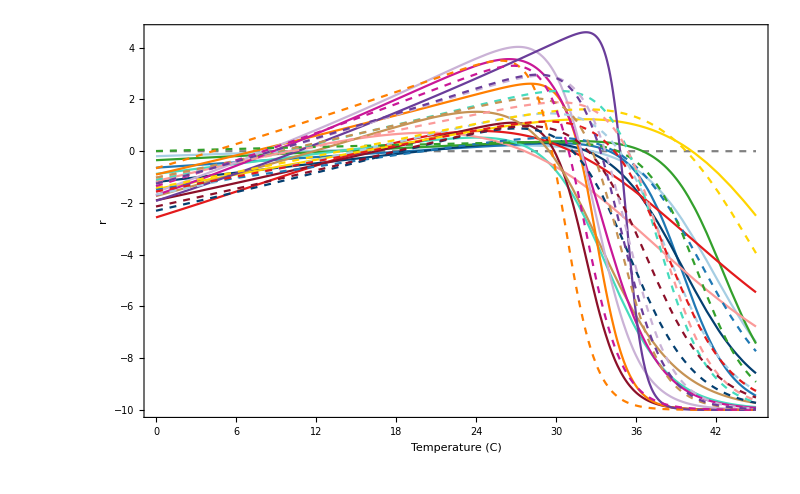

```mathematica
Clear["Global`*"]

TPCparamsRaw=Import["~/PNAS_Wieczynski_etal_2021_Master/data/TPC_model_parameters.csv"];
TPCparamsRawEst=Import["~/PNAS_Wieczynski_etal_2021_Master/data/TPC_model_parameters_est.csv"];
traitsRaw=Import["~/PNAS_Wieczynski_etal_2021_Master/data/traits_summary.csv"];
demoRaw=Import["~/PNAS_Wieczynski_etal_2021_Master/data/demo_parameters.csv"];
sppOrder={"Paramecium bursaria","Paramecium multimicronucleatum","Euplotes sp.","Blepharisma sp.","Urocentrum turbo","Colpidium striatum","Paramecium aurelia","Paramecium caudatum","Tillina magna","Halteria grandinella","Cyclidium glaucoma","Colpoda steinii","Glaucoma sp.","Tetrahymena pyriformis"};
nSpp=Length[sppOrder];
sppColors=RGBColor/@{"#A6CEE3","#1F78B4","#043f70","#33A02C","#46DBBD","#FB9A99","#E31A1C","#8c1029","#FFD500","#C69354","#FF7F00","#c91797","#CAB2D6","#6A3D9A"}
TPCparams=Table[Flatten[Select[TPCparamsRaw,#[[1]]==i&]],{i,sppOrder}];
TPCparamsPredicted=Table[Flatten[Select[TPCparamsRawEst,#[[1]]==i&]],{i,sppOrder}];
traits=Table[Flatten[Select[traitsRaw,#[[1]]==i&]],{i,sppOrder}];
Style["Empirical TPC parameters:",Bold]
Grid[Join[{TPCparamsRaw[[1]]},TPCparams],Alignment->Right]
Style["Trait-based (predicted) TPC parameters:",Bold]
Grid[Join[{TPCparamsRawEst[[1]]},TPCparamsPredicted],Alignment->Right]

TPCeqn[T_,a_,Ea_,Ed_,Th_]:=Exp[a+(Ea/(8.6*10^-5))*(1/298.15-1/(T+273.15))-Log[1+Exp[(Ed/(8.6*10^-5))*(1/Th-1/(T+273.15))]]]-10;
TPCfunc[T_,SpNum_,TPCversion_]:=TPCeqn@@Join[{T},If[TPCversion=="empirical",TPCparams[[SpNum,2;;5]],TPCparamsPredicted[[SpNum,10;;13]]]];

p1=Plot[(0*#)&[T],{T,0,45},PlotStyle->{Gray,Dashed},Axes->False,Frame->{{True,False},{True,False}},FrameTicksStyle->Directive[18],FrameLabel->{Style["Temperature (C)",16],Style["r",16]},ImageSize->800];
p2=Plot[Evaluate[Table[TPCfunc[T,i,"empirical"],{i,nSpp}]],{T,0,45},PlotStyle->sppColors];
p3=Plot[Evaluate[Table[TPCfunc[T,i,"predicted"],{i,nSpp}]],{T,0,45},PlotStyle->Table[{sppColors[[i]],Dashed},{i,Length[sppColors]}]];
Show[p1,p2,p3,PlotRange->{{0,43},{-1,Automatic}}]
```

## Numerical equilibria | multi-species w/ TPCs

### model functions

```mathematica
TPCeqn[T_,a_,Ea_,Ed_,Th_]:=Exp[a+(Ea/(8.6*10^-5))*(1/298.15-1/(T+273.15))-Log[1+Exp[(Ed/(8.6*10^-5))*(1/Th-1/(T+273.15))]]]-10;
TPCfunc[T_,SpNum_,TPCversion_]:=TPCeqn@@Join[{T},If[TPCversion=="empirical",TPCparams[[SpNum,2;;5]],TPCparamsPredicted[[SpNum,10;;13]]]];
feasibleSpp[sppInit_,T_,δ_,TPCversion_]:=If[TPCfunc[T,#,TPCversion]-δ>0,#,Nothing]&/@sppInit;

eqns[T_,α_,αversion_,δ_,sppSet_,sppInit_,TPCversion_,Kversion_]:=Module[{feasSpp,tempSpp,tempNSpp,αValues,kTotal,kValues,αMatrix},
feasSpp=feasibleSpp[sppInit,T,δ,TPCversion];
tempSpp=Which[sppSet=="all",sppInit,sppSet=="feasible",feasSpp];
tempNSpp=Length[tempSpp];
αValues=Table[If[i==j,1,If[αversion=="constant",α,RandomVariate[NormalDistribution[α,0.001],1]]],{i,tempNSpp},{j,tempNSpp}];
kTotal=If[TPCversion=="empirical",Total[demoRaw[[2;;,5]]],Total[TPCparamsPredicted[[;;,14]]]];

kValues=If[Kversion=="empirical",
If[TPCversion=="empirical",#/kTotal&/@demoRaw[[2;;,5]][[tempSpp]],#/kTotal&/@TPCparamsPredicted[[;;,14]][[tempSpp]]],
ConstantArray[1,tempNSpp]];

αMatrix=Table["("<>ToString[αValues[[i,j]]]<>"*"<>"n"<>ToString[tempSpp[[j]]]<>"/"<>ToString[kValues[[i]]]<>")",{i,tempNSpp},{j,tempNSpp}];
Table[ToString[TPCfunc[T,tempSpp[[i]],TPCversion]]<>"*n"<>ToString[tempSpp[[i]]]<>"*(1-("<>ToString[Total[αMatrix[[i]]]]<>"))-"<>ToString[δ]<>"*n"<>ToString[tempSpp[[i]]],{i,1,Length[tempSpp]}]
]

eqFunc[T_,α_,αversion_,δ_,sppSet_,sppInit_,TPCversion_,Kversion_]:=Module[{stateVarsInit,tempSpp,stateVars,sols1,sols2,sols,persistenceTest},
stateVarsInit=Table["n"<>ToString[i],{i,sppInit}];
tempSpp=feasibleSpp[sppInit,T,δ,TPCversion];
stateVars=Table[{"n"<>ToString[i],1},{i,tempSpp}];
sols1=If[Length[stateVars]==0,{Null->Null},FindRoot[ToExpression[#<>"==0"&/@eqns[T,α,αversion,δ,"feasible",sppInit,TPCversion,Kversion]]//Simplify//Rationalize,ToExpression[stateVars]]]//Quiet;
sols2=sols1/.x_/;NumericQ[x]:>Round[x,10^-6]//N;
sols=Select[sols2,#[[2]]>0&];
persistenceTest=Table[{i,Select[sols,#[[1]]==ToExpression[i]&]},{i,stateVarsInit}];
Table[If[Length[persistenceTest[[i,2]]]==1,persistenceTest[[i,2,1]],ToExpression[persistenceTest[[i,1]]]->0],{i,Length[persistenceTest]}]
]
```

### calculate equilibria for range of parameters

Small version (Figures 5/S4 A & E-G):

```mathematica
time1=SessionTime[];

Temps=Range[7,41,0.1];(* choose temperature range *)
αs={0.01(*, 0.1,1.*)};(* choose competition parameter set *)
δs={0.01,0.1(*,0.5*),1.};(* choose mortality parameter set *)
αversion="constant";(* choose "constant" or "random" *)
TPCversion="empirical";(* choose "empirical" or "predicted" *)
Kversion="empirical";(* choose "empirical" or "constant" *)
sppInit=Range[1,Length[sppOrder]](*{1,2,6,7,8,9,10,11,13,14}*);(* choose initial species set: 
For comparison with experimental communities (Figures 5/S4 E-G) use {1,2,6,7,8,9,10,11,13,14}, otherwise use Range[1,Length[sppOrder]] *)

out=Flatten[Table[Flatten[{n,T,α,δ,eqFunc[T,α,αversion,δ,sppInit,sppInit,TPCversion,Kversion][[;;,2]]}],{n,If[αversion=="constant",1,100]},{T,Temps},{α,αs},{δ,δs}],3];

"Computing time (s): "<>ToString[SessionTime[]-time1]
```

Computing time (s): 12.110486

export model output

```mathematica
Export["~/PNAS_Wieczynski_etal_2021_Master/data/model_rawdata_small.csv",Prepend[out,Join[{"n","Temperature","alpha","delta"},sppOrder[[sppInit]]]]]
```

Large version (Figures 5/S4 B-D):

```mathematica
time1=SessionTime[];

Temps=N[Subdivide[7,41,999]];(* choose temperature range *)
iTemps=Partition[Temps,10];

Do[
iT=iTemps[[i]];
αs={0.01};(* choose competition parameter set *)
δs=Range[0.001,1,0.001];(* choose mortality parameter set *)
sppInit=Range[1,Length[sppOrder]];(* choose initial species set *)
αversion="constant";(* choose "constant" or "random" *)
TPCversion="empirical";(* choose "empirical" or "predicted" *)
Kversion="empirical";(* choose "empirical" or "constant" *)

out=Flatten[Table[{T,α,δ,eqFunc[T,α,αversion,δ,sppInit,sppInit,TPCversion,Kversion][[;;,2]]},{T,iT},{α,αs},{δ,δs}],2];
Export["~/PNAS_Wieczynski_etal_2021_Master/data/temp/"<>ToString[i]<>"_model_rawdata_temp.csv",out];

,{i,Length[iTemps]}]

"Computing time (s): "<>ToString[SessionTime[]-time1]
```

export model output

```mathematica
files=FileNames["~/PNAS_Wieczynski_etal_2021_Master/data/temp/*_model_rawdata_temp.csv"];
data=Prepend[Flatten[#]&/@ToExpression[Flatten[Import[#,"CSV"]&/@files,1]],Join[{"Temperature","alpha","delta"},sppOrder]];

Export["~/PNAS_Wieczynski_etal_2021_Master/data/model_rawdata_large.csv",data]
```

## Network diagrams

```mathematica
transformFunc[data_]:=Module[{temp1,temp2,temp3},
temp1=If[#>0,Log10[#],0]&/@data;
temp2=Select[temp1,#≠0&];
temp3=If[#≠0,Rescale[#,{-5,0},{0,.7}],0]&/@temp1;
temp3
]

commNetwork[sppInit_,T_,α_,δ_]:=Module[{colors,nodes,sols,stateVars,equilibrium,feasMatrix,commMatrix,edgeMatrix,edgeIDs,edges,edgeWeights,edgeStyles,nodeWeights,nodeStyles,nodeShapes,annotations},
colors=sppColors;
nodes=Sort[sppInit];
sols=eqFunc[T,α,δ,nodes];
stateVars=sols[[;;,1]];
equilibrium=sols[[;;,2]];
feasMatrix=Table[Sign[equilibrium[[i]]]*Sign[equilibrium[[j]]],{i,1,Length[nodes]},{j,1,Length[nodes]}];
commMatrix=D[ToExpression[eqns[T,α,δ,"all",nodes]],{ToExpression[stateVars]}]/.sols;
edgeMatrix=feasMatrix*commMatrix;
edgeIDs=Permutations[nodes,{2}];
edges=#[[1]]->#[[2]]&/@edgeIDs;
edgeWeights=0.6*Abs[edgeMatrix[[#[[2]],#[[1]]]]&/@Permutations[Range[1,Length[nodes]],{2}]]/.{0.->-1};
edgeStyles={colors[[edges[[#,1]]]],Thickness[edgeWeights[[#]]],CapForm["Round"]}&/@Range[1,Length[edges]];
nodeWeights=transformFunc[equilibrium];
nodeStyles={colors[[nodes[[#]]]],EdgeForm[{Thickness[0.01],White,Opacity[1]}]}&/@Range[1,Length[nodes]];
nodeShapes=If[nodeWeights[[#]]==0,"",Automatic]&/@Range[Length[nodes]];
Graph[edges,DirectedEdges->True,EdgeShapeFunction->"Line",EdgeStyle->Thread[edges->edgeStyles],VertexSize->Thread[nodes->nodeWeights],VertexShape->Thread[nodes->nodeShapes],VertexStyle->Thread[nodes->nodeStyles],PerformanceGoal->"Quality",ImageSize->300]
]
commNetwork[Range[1,Length[sppOrder]],34,0.01,1.0]
```

-Graphics-

### export network graphs

```mathematica
Export["~/PNAS_Wieczynski_etal_2021_Master/graphics/raw_graphics/network.svg",GraphicsRow[commNetwork[Range[1,Length[sppOrder]],#,0.01,0.1]&/@{10,16,22,28,34}]]
```